```mathematica
PerBucket=Association[];
Table[PerBucket[allGraphs4[k,"vertexsets"]]={},{k,Keys[allGraphs4]}];
Table[PerBucket[allGraphs4[k,"vertexsets"]]=Append[PerBucket[allGraphs4[k,"vertexsets"]],k],{k,Keys[allGraphs4]}];
Length[PerBucket]
```

15

```mathematica
42
```

42

```mathematica
PerBucketPos=Association[];
Table[PerBucketPos[n]=Select[PerBucket[n],ToString[allGraphs4[#,"comp"]]=="Greater"&],{n,Keys[PerBucket]}];
```

```mathematica
TableForm[Table[SetsToSymbol2[n]->Tally[Table[allGraphs4[k,"comp"],{k,PerBucket[n]}]],{n,Keys[PerBucket]}]];
```

```mathematica
TableForm[Table[SetsToSymbol2[n]->Tally[Table[allGraphs4[k,"comp"],{k,PerBucketPos[n]}]],{n,Keys[PerBucketPos]}]];
```

```mathematica
Product[m,{m,Table[Length[PerBucket[k]],{k,Keys[PerBucket]}]}]
```

2147483648

```mathematica
1461401637330902918203684832716283019644932442976
```

1461401637330902918203684832716283019644932442976

```mathematica
Log[2,1461401637330902918203684832716283019644932442976]
```

Log[1461401637330902918203684832716283019644932442976]/Log[2]

```mathematica
Table[Log[2,Length[PerBucket[k]]],{k,Keys[PerBucket]}]//Tally//Sort
```

{{0,1},{1,7},{3,6},{6,1}}

```mathematica
{{0,1},{1,14},{3,24},{6,10},{10,1}}
```

{{0,1},{1,14},{3,24},{6,10},{10,1}}

```mathematica
randoms =Sort[Table[First[RandomSample[PerBucketPos[k],1]],{k,Keys[PerBucketPos]}],CompareSymbols[SetsToSymbol2[allGraphs4[#1,"vertexsets"]],SetsToSymbol2[allGraphs4[#2,"vertexsets"]]]&]
```

{325,365,22,276,577,414,391,488,168,72,26,666,546,473,728}

```mathematica
{22602,26609,1102,16,26820,22032,9048,40122,33074,4347,29920,26842,29328,9148,49208,39388,41640,13232,14016,13248,4640,31194,11244,21410,4132,1872,9844,666,29706,7034,42974,43902,49963,17441,34439,12407,39392,42976,43908,49972,13340,17468,14748,4920,32684,2124,29888,48288,44492,42232,39014,49048}
```

{22602,26609,1102,16,26820,22032,9048,40122,33074,4347,29920,26842,29328,9148,49208,39388,41640,13232,14016,13248,4640,31194,11244,21410,4132,1872,9844,666,29706,7034,42974,43902,49963,17441,34439,12407,39392,42976,43908,49972,13340,17468,14748,4920,32684,2124,29888,48288,44492,42232,39014,49048}

```mathematica
randoms=RandomSample[PerBucketPos[Table[{k},{k,1,4}]],42]
```

{337,270,243,324,247,84,355,91,12,118,121,282,39,255,327,361,9,1,283,81,354,333,253,31,28,4,280,109,244,360,252,117,112,246,10,352,37,328,13,279,3,256}

```mathematica
{19720,9004,28443,2187,26426,823,20493,9404,20044,29430,6840,2466,7374,849,22923,2414,26338,7434,27300,7640,28422,2423,22962,6844,2942,22680,20412,26244,29170,1046,27243,810,6471,344,3006,29164,29244,19696,8776,22142,6498,22198,22879,7299,27297,28442,9001,7443,22638,8778,28448,2307}
```

{19720,9004,28443,2187,26426,823,20493,9404,20044,29430,6840,2466,7374,849,22923,2414,26338,7434,27300,7640,28422,2423,22962,6844,2942,22680,20412,26244,29170,1046,27243,810,6471,344,3006,29164,29244,19696,8776,22142,6498,22198,22879,7299,27297,28442,9001,7443,22638,8778,28448,2307}

```mathematica
Table[Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]],{k,randoms}]
```

{-Graphics-337,-Graphics-270,-Graphics-243,-Graphics-324,-Graphics-247,-Graphics-84,-Graphics-355,-Graphics-91,-Graphics-12,-Graphics-118,-Graphics-121,-Graphics-282,-Graphics-39,-Graphics-255,-Graphics-327,-Graphics-361,-Graphics-9,-Graphics-1,-Graphics-283,-Graphics-81,-Graphics-354,-Graphics-333,-Graphics-253,-Graphics-31,-Graphics-28,-Graphics-4,-Graphics-280,-Graphics-109,-Graphics-244,-Graphics-360,-Graphics-252,-Graphics-117,-Graphics-112,-Graphics-246,-Graphics-10,-Graphics-352,-Graphics-37,-Graphics-328,-Graphics-13,-Graphics-279,-Graphics-3,-Graphics-256}

```mathematica
PartitionToSymbol4[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["r"<>end]]
```

```mathematica
randomSyms=Sort[Table[PartitionToSymbol4[allGraphs4[k,"vertexsets"]],{k,randoms}],CompareSymbols]
```

{r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4,r1x2x3x4}

```mathematica
{r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4}
```

{r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4,r1x2x3x4x4}

```mathematica
syms=Sort[Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}],CompareSymbols]
```

{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v12x34,v13x24,v14x23,v1x234,v123x4,v124x3,v134x2,v1234}

```mathematica
{v1x2x3x4x4,v1x2x3x44,v1x2x34x4,v1x2x34x4,v1x23x4x4,v1x24x3x4,v1x24x3x4,v12x3x4x4,v13x2x4x4,v14x2x3x4,v14x2x3x4,v1x23x44,v1x24x34,v1x24x34,v12x3x44,v12x34x4,v12x34x4,v13x2x44,v13x24x4,v13x24x4,v14x2x34,v14x23x4,v14x24x3,v14x2x34,v14x23x4,v14x24x3,v1x2x344,v1x234x4,v1x234x4,v1x244x3,v123x4x4,v124x3x4,v124x3x4,v134x2x4,v134x2x4,v144x2x3,v12x344,v123x44,v124x34,v124x34,v13x244,v134x24,v134x24,v14x234,v144x23,v14x234,v1x2344,v1234x4,v1234x4,v1244x3,v1344x2,v12344}
```

{v1x2x3x4x4,v1x2x3x44,v1x2x34x4,v1x2x34x4,v1x23x4x4,v1x24x3x4,v1x24x3x4,v12x3x4x4,v13x2x4x4,v14x2x3x4,v14x2x3x4,v1x23x44,v1x24x34,v1x24x34,v12x3x44,v12x34x4,v12x34x4,v13x2x44,v13x24x4,v13x24x4,v14x2x34,v14x23x4,v14x24x3,v14x2x34,v14x23x4,v14x24x3,v1x2x344,v1x234x4,v1x234x4,v1x244x3,v123x4x4,v124x3x4,v124x3x4,v134x2x4,v134x2x4,v144x2x3,v12x344,v123x44,v124x34,v124x34,v13x244,v134x24,v134x24,v14x234,v144x23,v14x234,v1x2344,v1234x4,v1234x4,v1244x3,v1344x2,v12344}

```mathematica
randomRep2=Table[PartitionToSymbol4[allGraphs4[k,"vertexsets"]]->Tooltip[Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]],allGraphs4[k,"compwhy"]],{k,randoms}];
```

```mathematica
randommat=Table[PartitionToSymbol4[allGraphs4[k,"vertexsets"]]==allGraphs4[k,"colofour"],{k,randoms}];TableForm[randommat];
```

```mathematica
randomfullsol=First[Solve[randommat,syms]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{v1x2x3x4→r1x2x3x4,v1x2x34→0,v1x23x4→0,v1x24x3→0,v12x3x4→0,v13x2x4→0,v14x2x3→0,v12x34→0,v13x24→0,v14x23→0,v1x234→0,v123x4→0,v124x3→0,v134x2→0}

```mathematica
{v1x2x3x4x4->r1x2x3x4x4,v1x2x3x44->0,v1x2x34x4->0,v1x2x34x4->0,v1x23x4x4->0,v1x24x3x4->0,v1x24x3x4->0,v12x3x4x4->0,v13x2x4x4->0,v14x2x3x4->0,v14x2x3x4->0,v1x23x44->0,v1x24x34->0,v1x24x34->0,v12x3x44->0,v12x34x4->0,v12x34x4->0,v13x2x44->0,v13x24x4->0,v13x24x4->0,v14x2x34->0,v14x23x4->0,v14x24x3->0,v14x2x34->0,v14x23x4->0,v14x24x3->0,v1x2x344->0,v1x234x4->0,v1x234x4->0,v1x244x3->0,v123x4x4->0,v124x3x4->0,v124x3x4->0,v134x2x4->0,v134x2x4->0,v144x2x3->0,v12x344->0,v123x44->0,v124x34->0,v124x34->0,v134x24->0,v134x24->0,v14x234->0,v14x234->0,v1x2344->-v13x244,v1234x4->0}
```

{v1x2x3x4x4→r1x2x3x4x4,v1x2x3x44→0,v1x2x34x4→0,v1x2x34x4→0,v1x23x4x4→0,v1x24x3x4→0,v1x24x3x4→0,v12x3x4x4→0,v13x2x4x4→0,v14x2x3x4→0,v14x2x3x4→0,v1x23x44→0,v1x24x34→0,v1x24x34→0,v12x3x44→0,v12x34x4→0,v12x34x4→0,v13x2x44→0,v13x24x4→0,v13x24x4→0,v14x2x34→0,v14x23x4→0,v14x24x3→0,v14x2x34→0,v14x23x4→0,v14x24x3→0,v1x2x344→0,v1x234x4→0,v1x234x4→0,v1x244x3→0,v123x4x4→0,v124x3x4→0,v124x3x4→0,v134x2x4→0,v134x2x4→0,v144x2x3→0,v12x344→0,v123x44→0,v124x34→0,v124x34→0,v134x24→0,v134x24→0,v14x234→0,v14x234→0,v1x2344→-v13x244,v1234x4→0}

```mathematica
TableForm[
Table[
Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]]->
{allGraphs4[k,"colofour"]/.randomfullsol/.randomRep2,allGraphs4[k,"colofour"]/.randomfullsol},
{k,allGraphs4AtomKeys}
]
]
```

-Graphics-364→{-Graphics-337,r1x2x3x4}
-Graphics-365→{0,0}
-Graphics-367→{0,0}
-Graphics-373→{0,0}
-Graphics-377→{0,0}
-Graphics-391→{0,0}
-Graphics-400→{0,0}
-Graphics-445→{0,0}
-Graphics-448→{0,0}
-Graphics-473→{0,0}
-Graphics-607→{0,0}
-Graphics-608→{0,0}
-Graphics-637→{0,0}
-Graphics-697→{0,0}
-Graphics-728→{v1234,v1234}

```mathematica
{{-Graphics-29424->{-Graphics-19720,r1x2x3x4x4}}, {-Graphics-29424->{0,0}}, {-Graphics-29427->{0,0}}, {-Graphics-29433->{0,0}}, {-Graphics-29437->{0,0}}, {-Graphics-29441->{0,0}}, {-Graphics-29460->{0,0}}, {-Graphics-29604->{0,0}}, {-Graphics-29608->{0,0}}, {-Graphics-29633->{0,0}}, {-Graphics-29767->{0,0}}, {-Graphics-29768->{0,0}}, {-Graphics-29797->{0,0}}, {-Graphics-29847->{0,0}}, {-Graphics-29888->{-v13x244,-v13x244}}, {-Graphics-30243->{0,0}}, {-Graphics-30262->{0,0}}, {-Graphics-30334->{0,0}}, {-Graphics-30496->{0,0}}, {-Graphics-30486->{0,0}}, {-Graphics-31711->{0,0}}, {-Graphics-31714->{0,0}}, {-Graphics-31738->{0,0}}, {-Graphics-31944->{0,0}}, {-Graphics-31984->{0,0}}, {-Graphics-32441->{0,0}}, {-Graphics-32684->{v144x23,v144x23}}, {-Graphics-36084->{0,0}}, {-Graphics-36086->{0,0}}, {-Graphics-36112->{0,0}}, {-Graphics-36166->{0,0}}, {-Graphics-36194->{v13x244,v13x244}}, {-Graphics-36817->{0,0}}, {-Graphics-36898->{0,0}}, {-Graphics-38281->{0,0}}, {-Graphics-38308->{0,0}}, {-Graphics-39014->{v1344x2,v1344x2}}, {-Graphics-49207->{0,0}}, {-Graphics-49208->{0,0}}, {-Graphics-49210->{0,0}}, {-Graphics-49216->{0,0}}, {-Graphics-49220->{0,0}}, {-Graphics-49963->{0,0}}, {-Graphics-49972->{0,0}}, {-Graphics-41474->{0,0}}, {-Graphics-41478->{0,0}}, {-Graphics-42232->{v1244x3,v1244x3}}, {-Graphics-46011->{0,0}}, {-Graphics-46012->{0,0}}, {-Graphics-46770->{0,0}}, {-Graphics-48288->{v1234x4,v1234x4}}, {-Graphics-49048->{v12344,v12344}}}
```

{-Graphics-29424→{-Graphics-19720,r1x2x3x4x4},-Graphics-29424→{0,0},-Graphics-29427→{0,0},-Graphics-29433→{0,0},-Graphics-29437→{0,0},-Graphics-29441→{0,0},-Graphics-29460→{0,0},-Graphics-29604→{0,0},-Graphics-29608→{0,0},-Graphics-29633→{0,0},-Graphics-29767→{0,0},-Graphics-29768→{0,0},-Graphics-29797→{0,0},-Graphics-29847→{0,0},-Graphics-29888→{-v13x244,-v13x244},-Graphics-30243→{0,0},-Graphics-30262→{0,0},-Graphics-30334→{0,0},-Graphics-30496→{0,0},-Graphics-30486→{0,0},-Graphics-31711→{0,0},-Graphics-31714→{0,0},-Graphics-31738→{0,0},-Graphics-31944→{0,0},-Graphics-31984→{0,0},-Graphics-32441→{0,0},-Graphics-32684→{v144x23,v144x23},-Graphics-36084→{0,0},-Graphics-36086→{0,0},-Graphics-36112→{0,0},-Graphics-36166→{0,0},-Graphics-36194→{v13x244,v13x244},-Graphics-36817→{0,0},-Graphics-36898→{0,0},-Graphics-38281→{0,0},-Graphics-38308→{0,0},-Graphics-39014→{v1344x2,v1344x2},-Graphics-49207→{0,0},-Graphics-49208→{0,0},-Graphics-49210→{0,0},-Graphics-49216→{0,0},-Graphics-49220→{0,0},-Graphics-49963→{0,0},-Graphics-49972→{0,0},-Graphics-41474→{0,0},-Graphics-41478→{0,0},-Graphics-42232→{v1244x3,v1244x3},-Graphics-46011→{0,0},-Graphics-46012→{0,0},-Graphics-46770→{0,0},-Graphics-48288→{v1234x4,v1234x4},-Graphics-49048→{v12344,v12344}}

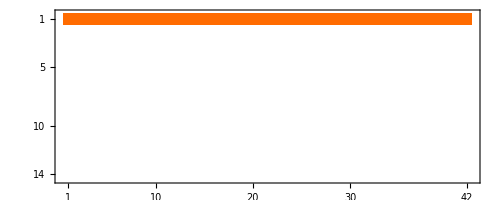

```mathematica
rmat=  Map[
Table[Coefficient[#[[2]],t],{t,randomSyms}]&,
randomfullsol];MatrixPlot[rmat]
```

```mathematica
UpperTriangularize[rmat]==rmat
```

True

```mathematica
MatrixRank[rmat]
```

1

```mathematica
Inverse[rmat]//MatrixPlot
```

Inverse::matsq: Argument … at position 1 is not a non-empty square matrix.

MatrixPlot::mat0: Argument … at position 1 is not a matrix.

MatrixPlot[Inverse[{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]]

```mathematica
Inverse[rmat]//Total//Total
```

Inverse::matsq: Argument … at position 1 is not a non-empty square matrix.

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## Orthogonalize dd

```mathematica
syms=Sort[Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}],CompareSymbols]
```

{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v12x34,v13x24,v14x23,v1x234,v123x4,v124x3,v134x2,v1234}

```mathematica
{v1x2x3x4x4,v1x2x3x44,v1x2x34x4,v1x2x34x4,v1x23x4x4,v1x24x3x4,v1x24x3x4,v12x3x4x4,v13x2x4x4,v14x2x3x4,v14x2x3x4,v1x23x44,v1x24x34,v1x24x34,v12x3x44,v12x34x4,v12x34x4,v13x2x44,v13x24x4,v13x24x4,v14x2x34,v14x23x4,v14x24x3,v14x2x34,v14x23x4,v14x24x3,v1x2x344,v1x234x4,v1x234x4,v1x244x3,v123x4x4,v124x3x4,v124x3x4,v134x2x4,v134x2x4,v144x2x3,v12x344,v123x44,v124x34,v124x34,v13x244,v134x24,v134x24,v14x234,v144x23,v14x234,v1x2344,v1234x4,v1234x4,v1244x3,v1344x2,v12344}
```

{v1x2x3x4x4,v1x2x3x44,v1x2x34x4,v1x2x34x4,v1x23x4x4,v1x24x3x4,v1x24x3x4,v12x3x4x4,v13x2x4x4,v14x2x3x4,v14x2x3x4,v1x23x44,v1x24x34,v1x24x34,v12x3x44,v12x34x4,v12x34x4,v13x2x44,v13x24x4,v13x24x4,v14x2x34,v14x23x4,v14x24x3,v14x2x34,v14x23x4,v14x24x3,v1x2x344,v1x234x4,v1x234x4,v1x244x3,v123x4x4,v124x3x4,v124x3x4,v134x2x4,v134x2x4,v144x2x3,v12x344,v123x44,v124x34,v124x34,v13x244,v134x24,v134x24,v14x234,v144x23,v14x234,v1x2344,v1234x4,v1234x4,v1244x3,v1344x2,v12344}

```mathematica
symsNull=Sort[Table[allGraphs4[k,"colofourrealnull"],{k,allGraphs4NullAtomKeys}],CompareSymbols]
```

{n1x2x3x4,n1x2x34,n1x23x4,n1x24x3,n12x3x4,n13x2x4,n14x2x3,n12x34,n13x24,n14x23,n1x234,n123x4,n124x3,n134x2,n1234}

```mathematica
{n1x2x3x4x4,n1x2x3x44,n1x2x34x4,n1x2x34x4,n1x23x4x4,n1x24x3x4,n1x24x3x4,n12x3x4x4,n13x2x4x4,n14x2x3x4,n14x2x3x4,n1x23x44,n1x24x34,n1x24x34,n12x3x44,n12x34x4,n12x34x4,n13x2x44,n13x24x4,n13x24x4,n14x2x34,n14x23x4,n14x24x3,n14x2x34,n14x23x4,n14x24x3,n1x2x344,n1x234x4,n1x234x4,n1x244x3,n123x4x4,n124x3x4,n124x3x4,n134x2x4,n134x2x4,n144x2x3,n12x344,n123x44,n124x34,n124x34,n13x244,n134x24,n134x24,n14x234,n144x23,n14x234,n1x2344,n1234x4,n1234x4,n1244x3,n1344x2,n12344}
```

{n1x2x3x4x4,n1x2x3x44,n1x2x34x4,n1x2x34x4,n1x23x4x4,n1x24x3x4,n1x24x3x4,n12x3x4x4,n13x2x4x4,n14x2x3x4,n14x2x3x4,n1x23x44,n1x24x34,n1x24x34,n12x3x44,n12x34x4,n12x34x4,n13x2x44,n13x24x4,n13x24x4,n14x2x34,n14x23x4,n14x24x3,n14x2x34,n14x23x4,n14x24x3,n1x2x344,n1x234x4,n1x234x4,n1x244x3,n123x4x4,n124x3x4,n124x3x4,n134x2x4,n134x2x4,n144x2x3,n12x344,n123x44,n124x34,n124x34,n13x244,n134x24,n134x24,n14x234,n144x23,n14x234,n1x2344,n1234x4,n1234x4,n1244x3,n1344x2,n12344}

```mathematica
Coeff[k_]:=Table[Coefficient[allGraphs4[k,"colofour"],t],{t,syms}]
```

```mathematica
CoeffNull[k_]:=Table[Coefficient[allGraphs4[k,"colofourrealnull"],t],{t,symsNull}]
```

```mathematica
syms
```

{v1x2x3x4,v1x2x34,v1x23x4,v1x24x3,v12x3x4,v13x2x4,v14x2x3,v12x34,v13x24,v14x23,v1x234,v123x4,v124x3,v134x2,v1234}

```mathematica
{v1x2x3x4x4,v1x2x3x44,v1x2x34x4,v1x2x34x4,v1x23x4x4,v1x24x3x4,v1x24x3x4,v12x3x4x4,v13x2x4x4,v14x2x3x4,v14x2x3x4,v1x23x44,v1x24x34,v1x24x34,v12x3x44,v12x34x4,v12x34x4,v13x2x44,v13x24x4,v13x24x4,v14x2x34,v14x23x4,v14x24x3,v14x2x34,v14x23x4,v14x24x3,v1x2x344,v1x234x4,v1x234x4,v1x244x3,v123x4x4,v124x3x4,v124x3x4,v134x2x4,v134x2x4,v144x2x3,v12x344,v123x44,v124x34,v124x34,v13x244,v134x24,v134x24,v14x234,v144x23,v14x234,v1x2344,v1234x4,v1234x4,v1244x3,v1344x2,v12344}
```

{v1x2x3x4x4,v1x2x3x44,v1x2x34x4,v1x2x34x4,v1x23x4x4,v1x24x3x4,v1x24x3x4,v12x3x4x4,v13x2x4x4,v14x2x3x4,v14x2x3x4,v1x23x44,v1x24x34,v1x24x34,v12x3x44,v12x34x4,v12x34x4,v13x2x44,v13x24x4,v13x24x4,v14x2x34,v14x23x4,v14x24x3,v14x2x34,v14x23x4,v14x24x3,v1x2x344,v1x234x4,v1x234x4,v1x244x3,v123x4x4,v124x3x4,v124x3x4,v134x2x4,v134x2x4,v144x2x3,v12x344,v123x44,v124x34,v124x34,v13x244,v134x24,v134x24,v14x234,v144x23,v14x234,v1x2344,v1234x4,v1234x4,v1244x3,v1344x2,v12344}

```mathematica
Keys[PerBucket]
```

{{{1},{2},{3},{4}},{{1},{2},{3,4}},{{1},{2,4},{3}},{{1},{2,3},{4}},{{1},{2,3,4}},{{1,4},{2},{3}},{{1,4},{2,3}},{{1,3},{2},{4}},{{1,3},{2,4}},{{1,3,4},{2}},{{1,2},{3},{4}},{{1,2},{3,4}},{{1,2,4},{3}},{{1,2,3},{4}},{{1,2,3,4}}}

```mathematica
{{{1},{2},{3},{4},{4}},{{1},{2},{3},{4,4}},{{1},{2},{3,4},{4}},{{1},{2},{3,4},{4}},{{1},{2},{3,4,4}},{{1},{2,4},{3},{4}},{{1},{2,4},{3,4}},{{1},{2,4},{3},{4}},{{1},{2,4},{3,4}},{{1},{2,4,4},{3}},{{1},{2,3},{4},{4}},{{1},{2,3},{4,4}},{{1},{2,3,4},{4}},{{1},{2,3,4},{4}},{{1},{2,3,4,4}},{{1,4},{2},{3},{4}},{{1,4},{2},{3,4}},{{1,4},{2,4},{3}},{{1,4},{2,3},{4}},{{1,4},{2,3,4}},{{1,4},{2},{3},{4}},{{1,4},{2},{3,4}},{{1,4},{2,4},{3}},{{1,4},{2,3},{4}},{{1,4},{2,3,4}},{{1,4,4},{2},{3}},{{1,4,4},{2,3}},{{1,3},{2},{4},{4}},{{1,3},{2},{4,4}},{{1,3},{2,4},{4}},{{1,3},{2,4},{4}},{{1,3},{2,4,4}},{{1,3,4},{2},{4}},{{1,3,4},{2,4}},{{1,3,4},{2},{4}},{{1,3,4},{2,4}},{{1,3,4,4},{2}},{{1,2},{3},{4},{4}},{{1,2},{3},{4,4}},{{1,2},{3,4},{4}},{{1,2},{3,4},{4}},{{1,2},{3,4,4}},{{1,2,4},{3},{4}},{{1,2,4},{3,4}},{{1,2,4},{3},{4}},{{1,2,4},{3,4}},{{1,2,4,4},{3}},{{1,2,3},{4},{4}},{{1,2,3},{4,4}},{{1,2,3,4},{4}},{{1,2,3,4},{4}},{{1,2,3,4,4}}}
```

{{{1},{2},{3},{4},{4}},{{1},{2},{3},{4,4}},{{1},{2},{3,4},{4}},{{1},{2},{3,4},{4}},{{1},{2},{3,4,4}},{{1},{2,4},{3},{4}},{{1},{2,4},{3,4}},{{1},{2,4},{3},{4}},{{1},{2,4},{3,4}},{{1},{2,4,4},{3}},{{1},{2,3},{4},{4}},{{1},{2,3},{4,4}},{{1},{2,3,4},{4}},{{1},{2,3,4},{4}},{{1},{2,3,4,4}},{{1,4},{2},{3},{4}},{{1,4},{2},{3,4}},{{1,4},{2,4},{3}},{{1,4},{2,3},{4}},{{1,4},{2,3,4}},{{1,4},{2},{3},{4}},{{1,4},{2},{3,4}},{{1,4},{2,4},{3}},{{1,4},{2,3},{4}},{{1,4},{2,3,4}},{{1,4,4},{2},{3}},{{1,4,4},{2,3}},{{1,3},{2},{4},{4}},{{1,3},{2},{4,4}},{{1,3},{2,4},{4}},{{1,3},{2,4},{4}},{{1,3},{2,4,4}},{{1,3,4},{2},{4}},{{1,3,4},{2,4}},{{1,3,4},{2},{4}},{{1,3,4},{2,4}},{{1,3,4,4},{2}},{{1,2},{3},{4},{4}},{{1,2},{3},{4,4}},{{1,2},{3,4},{4}},{{1,2},{3,4},{4}},{{1,2},{3,4,4}},{{1,2,4},{3},{4}},{{1,2,4},{3,4}},{{1,2,4},{3},{4}},{{1,2,4},{3,4}},{{1,2,4,4},{3}},{{1,2,3},{4},{4}},{{1,2,3},{4,4}},{{1,2,3,4},{4}},{{1,2,3,4},{4}},{{1,2,3,4,4}}}

```mathematica
Monitor[Table[allGraphs4[k,"colofourvector"]=Coeff[k],{k,Keys[allGraphs4]}],k];
```

```mathematica
allGraphs4[0,"colofourvector"]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Monitor[Table[allGraphs4[k,"colofournullvector"]=CoeffNull[k],{k,Keys[allGraphs4]}],k]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,-1,-1,0,0,0,0,0,1,0,0,0},{1,0,0,0,-1,-1,-1,0,0,0,0,1,1,1,-1},{1,0,-1,0,-1,-1,-1,0,0,1,0,2,1,1,-2},{1,0,-1,-1,-1,-1,-1,0,1,1,1,2,2,1,-4},{1,-1,-1,-1,-1,-1,-1,1,1,1,2,2,2,2,-6},{0,1,0,0,0,0,0,-1,0,0,-1,0,0,-1,2},{0,0,0,1,0,0,0,0,-1,0,-1,0,-1,0,2},{1,-1,-1,0,-1,-1,-1,1,0,1,1,2,1,2,-4},{0,0,1,0,0,0,0,0,0,-1,0,-1,0,0,1},{0,0,1,0,0,0,0,0,0,-1,-1,-1,0,0,2},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1},{1,0,0,-1,-1,-1,-1,0,1,0,0,1,2,1,-2},{1,-1,0,-1,-1,-1,-1,1,1,0,1,1,2,2,-4},{0,0,0,1,0,0,0,0,-1,0,0,0,-1,0,1},{1,-1,0,0,-1,-1,-1,1,0,0,0,1,1,2,-2},{0,1,0,0,0,0,0,-1,0,0,0,0,0,-1,1},{0,0,0,0,0,0,1,0,0,0,0,0,-1,-1,1},{0,0,0,0,0,0,1,0,0,-1,0,0,-1,-1,2},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1},{1,0,-1,0,-1,-1,0,0,0,0,0,2,0,0,0},{1,0,-1,-1,-1,-1,0,0,1,0,1,2,1,0,-2},{1,-1,-1,-1,-1,-1,0,1,1,0,2,2,1,1,-4},{1,-1,-1,0,-1,-1,0,1,0,0,1,2,0,1,-2},{0,0,1,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,1,0,0,0,0,0,0,0,-1,-1,0,0,1},{1,0,0,-1,-1,-1,0,0,1,0,0,1,1,0,-1},{1,-1,0,-1,-1,-1,0,1,1,0,1,1,1,1,-3},{1,-1,0,0,-1,-1,0,1,0,0,0,1,0,1,-1},{0,0,0,0,0,1,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,-1,0,-1,1},{0,0,0,0,0,1,0,0,-1,0,0,-1,0,-1,2},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1},{0,0,0,0,0,1,0,0,-1,0,0,-1,0,0,1},{1,0,0,0,-1,0,-1,0,0,0,0,0,1,0,0},{1,0,-1,0,-1,0,-1,0,0,1,0,1,1,0,-1},{1,0,-1,-1,-1,0,-1,0,0,1,1,1,2,0,-2},{1,-1,-1,-1,-1,0,-1,1,0,1,2,1,2,1,-4},{0,0,0,1,0,0,0,0,0,0,-1,0,-1,0,1},{1,-1,-1,0,-1,0,-1,1,0,1,1,1,1,1,-3},{1,0,0,-1,-1,0,-1,0,0,0,0,0,2,0,0},{1,-1,0,-1,-1,0,-1,1,0,0,1,0,2,1,-2},{0,0,0,1,0,0,0,0,0,0,0,0,-1,0,0},{1,-1,0,0,-1,0,-1,1,0,0,0,0,1,1,-1},{0,0,0,0,0,0,1,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,1,0,0,-1,0,0,-1,0,1},{1,0,-1,0,-1,0,0,0,0,0,0,1,0,0,0},{1,0,-1,-1,-1,0,0,0,0,0,1,1,1,0,-1},{1,-1,-1,-1,-1,0,0,1,0,0,2,1,1,0,-2},{0,1,0,0,0,0,0,-1,0,0,-1,0,0,0,1},{1,-1,-1,0,-1,0,0,1,0,0,1,1,0,0,-1},{1,0,0,-1,-1,0,0,0,0,0,0,0,1,0,0},{1,-1,0,-1,-1,0,0,1,0,0,1,0,1,0,-1},{1,-1,0,0,-1,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,-1,-1,0,1},{0,0,0,0,1,0,0,-1,0,0,0,-1,-1,0,2},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1},{0,0,0,0,1,0,0,-1,0,0,0,-1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,-1,0,0,0,0,-1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,-1,-1,0,0,0,0,0,0,1,0},{1,0,-1,0,0,-1,-1,0,0,1,0,1,0,1,-1},{1,0,-1,-1,0,-1,-1,0,1,1,1,1,1,1,-3},{1,-1,-1,-1,0,-1,-1,0,1,1,2,1,1,2,-4},{0,1,0,0,0,0,0,0,0,0,-1,0,0,-1,1},{1,-1,-1,0,0,-1,-1,0,0,1,1,1,0,2,-2},{1,0,0,-1,0,-1,-1,0,1,0,0,0,1,1,-1},{1,-1,0,-1,0,-1,-1,0,1,0,1,0,1,2,-2},{1,-1,0,0,0,-1,-1,0,0,0,0,0,0,2,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,1,0,0,-1,0,0,0,-1,1},{1,0,-1,0,0,-1,0,0,0,0,0,1,0,0,0},{1,0,-1,-1,0,-1,0,0,1,0,1,1,0,0,-1},{1,-1,-1,-1,0,-1,0,0,1,0,2,1,0,1,-2},{0,0,0,1,0,0,0,0,-1,0,-1,0,0,0,1},{1,-1,-1,0,0,-1,0,0,0,0,1,1,0,1,-1},{1,0,0,-1,0,-1,0,0,1,0,0,0,0,0,0},{1,-1,0,-1,0,-1,0,0,1,0,1,0,0,1,-1},{0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0},{1,-1,0,0,0,-1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,1,0,0,-1,0,0,0,0,-1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{1,0,-1,0,0,0,-1,0,0,1,0,0,0,0,0},{1,0,-1,-1,0,0,-1,0,0,1,1,0,1,0,-1},{1,-1,-1,-1,0,0,-1,0,0,1,2,0,1,1,-2},{1,-1,-1,0,0,0,-1,0,0,1,1,0,0,1,-1},{0,0,1,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,-1,-1,0,0,0,1},{1,0,0,-1,0,0,-1,0,0,0,0,0,1,0,0},{1,-1,0,-1,0,0,-1,0,0,0,1,0,1,1,-1},{1,-1,0,0,0,0,-1,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,-1,-1,0,0,0,0,0,0,1,0,0,0,0},{1,-1,-1,-1,0,0,0,0,0,0,2,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,-1,0,0,0,0},{1,-1,-1,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{1,-1,0,-1,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[Total [Table[allGraphs4[m,"colofourvector"].allGraphs4[v,"colofourvector"],{v,Keys[allGraphs4]}]],{m,Keys[allGraphs4]}]//Sort//Tally
```

{{15,1},{22,4},{26,3},{37,4},{40,6},{41,3},{62,12},{64,1},{66,6},{84,6},{88,12},{104,6},{125,6},{144,12},{170,3},{184,4},{206,4},{210,12},{272,12},{276,3},{360,6},{485,1}}

```mathematica
Table[{Length[PerBucket[v]],MatrixRank[Table[allGraphs4[k,"colofourvector"],{k,PerBucket[v]}]]},{v,Keys[PerBucket]}]//Sort//Tally
```

{{{1,1},1},{{2,2},7},{{8,5},6},{{64,15},1}}

```mathematica
{{{1,1},1},{{2,2},14},{{8,4},24},{{64,14},10},{{1024,42},1}}
```

{{{1,1},1},{{2,2},14},{{8,4},24},{{64,14},10},{{1024,42},1}}

```mathematica
Table[SymbolToLabel[ SetsToSymbol2[v]]->{Length[PerBucket[v]],MatrixRank[Table[allGraphs4[k,"colofourvector"],{k,PerBucket[v]}]]},{v,Keys[PerBucket]}]
```

{1♁2♁3♁4→{64,15},1♁2♁34→{8,5},1♁24♁3→{8,5},1♁23♁4→{8,5},1♁234→{2,2},14♁2♁3→{8,5},14♁23→{2,2},13♁2♁4→{8,5},13♁24→{2,2},134♁2→{2,2},12♁3♁4→{8,5},12♁34→{2,2},124♁3→{2,2},123♁4→{2,2},1234→{1,1}}

## Finding a base in the first bucket

```mathematica
MatrixRank[Table[allGraphs4[k,"colofourvector"],{k,PerBucket[{{1},{2},{3},{4}}]}]]
```

15

```mathematica
mm=Sort[Table[allGraphs4[k,"colofourvector"],{k,
PerBucket[{{1},{2},{3},{4}}]}],FromDigits[Reverse[#1],2]<FromDigits[Reverse[#2],2]&]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,0,0,0,0,0,0,0},{1,1,0,1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{1,1,0,0,1,0,0,1,0,0,0,0,0,0,0},{1,1,1,0,1,0,0,1,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,1,0,0,0,0,0,0,0},{1,1,0,0,1,1,0,1,0,0,0,0,0,0,0},{1,1,0,0,1,0,1,1,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,1,0,0,0,0,0,0},{1,1,0,1,0,1,0,0,1,0,0,0,0,0,0},{1,0,1,1,0,1,0,0,1,0,0,0,0,0,0},{1,0,0,1,1,1,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,1,1,0,1,0,0,0,0,0,0},{1,1,0,1,1,1,0,1,1,0,0,0,0,0,0},{1,0,1,0,0,0,1,0,0,1,0,0,0,0,0},{1,1,1,0,0,0,1,0,0,1,0,0,0,0,0},{1,0,1,1,0,0,1,0,0,1,0,0,0,0,0},{1,0,1,0,1,0,1,0,0,1,0,0,0,0,0},{1,0,1,0,0,1,1,0,0,1,0,0,0,0,0},{1,1,1,0,1,0,1,1,0,1,0,0,0,0,0},{1,0,1,1,0,1,1,0,1,1,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,1,0,0,0,0},{1,1,1,1,1,0,0,1,0,0,1,0,0,0,0},{1,1,1,1,0,1,0,0,1,0,1,0,0,0,0},{1,1,1,1,0,0,1,0,0,1,1,0,0,0,0},{1,0,1,0,1,1,0,0,0,0,0,1,0,0,0},{1,1,1,0,1,1,0,1,0,0,0,1,0,0,0},{1,0,1,1,1,1,0,0,1,0,0,1,0,0,0},{1,0,1,0,1,1,1,0,0,1,0,1,0,0,0},{1,1,1,1,1,1,0,1,1,0,1,1,0,0,0},{1,0,0,1,1,0,1,0,0,0,0,0,1,0,0},{1,1,0,1,1,0,1,1,0,0,0,0,1,0,0},{1,0,0,1,1,1,1,0,1,0,0,0,1,0,0},{1,0,1,1,1,0,1,0,0,1,0,0,1,0,0},{1,1,1,1,1,0,1,1,0,1,1,0,1,0,0},{1,0,1,1,1,1,1,0,1,1,0,1,1,0,0},{1,1,0,0,0,1,1,0,0,0,0,0,0,1,0},{1,1,0,0,1,1,1,1,0,0,0,0,0,1,0},{1,1,0,1,0,1,1,0,1,0,0,0,0,1,0},{1,1,1,0,0,1,1,0,0,1,0,0,0,1,0},{1,1,1,1,0,1,1,0,1,1,1,0,0,1,0},{1,1,1,0,1,1,1,1,0,1,0,1,0,1,0},{1,1,0,1,1,1,1,1,1,0,0,0,1,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
mmbase=Block[{result={},currentRank=1,length=Length[mm],pos,attempt,rank,previousRank,keys},
keys=Table[First[
Select[Keys[allGraphs4],allGraphs4[#,"colofourvector"]==mm[[k]]&]
],
{k,1,length}
];
result={mm[[1]]};
While[currentRank≠15,
previousRank=currentRank;
For[pos=1,pos≤length,pos++,
If[True||ToString[allGraphs4[keys[pos],"comp"]]=="Greater"||keys[pos]==K4Key,
attempt=Append[result,mm[[pos]]];
rank=MatrixRank[attempt];
If[rank> currentRank,
result=attempt;
pos=length+1;
currentRank=rank
]
]
];
If[previousRank==currentRank, Interrupt[]]
];
result
]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{1,1,0,0,1,0,0,1,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,1,0,0,0,0,0,0},{1,0,1,0,0,0,1,0,0,1,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,1,0,0,0,0},{1,0,1,0,1,1,0,0,0,0,0,1,0,0,0},{1,0,0,1,1,0,1,0,0,0,0,0,1,0,0},{1,1,0,0,0,1,1,0,0,0,0,0,0,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

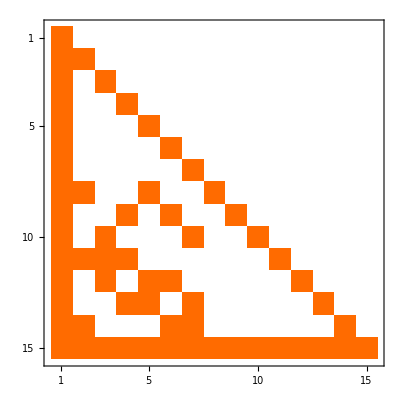

```mathematica
mmbase//MatrixPlot
```

```mathematica
mmbaseKeys=Monitor[Table[
First[
Select[Keys[allGraphs4],allGraphs4[#,"colofourvector"]==mmbase[[k]]&]
],{k,1,15}],k]
```

{364,363,355,361,121,283,337,120,280,328,351,31,91,255,0}

```mathematica
Table[Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]]->
With[{c=FindComplement[k,allGraphs4]},
Labeled[allGraphs4[c,"graph"],Style[c,ColourForKey[allGraphs4,c]]]],{k,mmbaseKeys}]
```

{-Graphics-364→-Graphics-0,-Graphics-363→-Graphics-1,-Graphics-355→-Graphics-9,-Graphics-361→-Graphics-3,-Graphics-121→-Graphics-243,-Graphics-283→-Graphics-81,-Graphics-337→-Graphics-27,-Graphics-120→-Graphics-244,-Graphics-280→-Graphics-84,-Graphics-328→-Graphics-36,-Graphics-351→-Graphics-13,-Graphics-31→-Graphics-333,-Graphics-91→-Graphics-273,-Graphics-255→-Graphics-109,-Graphics-0→-Graphics-364}

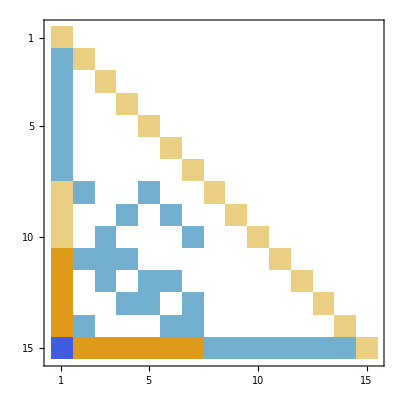

```mathematica
MatrixPlot[Inverse[mmbase]]
```

```mathematica
Det[Inverse[mmbase]]
```

1

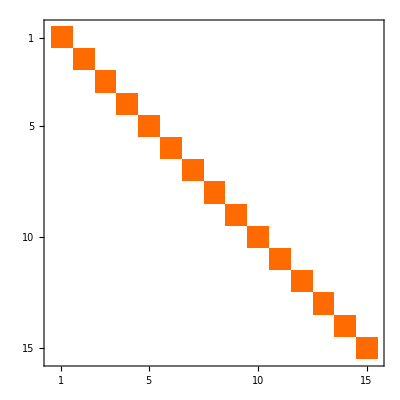
{-Graphics-,-Graphics-}

```mathematica
Map[MatrixPlot,HermiteDecomposition[Inverse[mmbase]]]
```

```mathematica
OrthogonalMatrixQ[mmbase]
```

False

```mathematica
Table[
Labeled[allGraphs4[searck,"graph"],Style[searck,ColourForKey[allGraphs4,searck]]],
{searck,Take[Keys[allGraphs4],40]}
]
```

{-Graphics-0,-Graphics-243,-Graphics-324,-Graphics-351,-Graphics-360,-Graphics-363,-Graphics-364,-Graphics-365,-Graphics-367,-Graphics-361,-Graphics-369,-Graphics-373,-Graphics-377,-Graphics-354,-Graphics-355,-Graphics-357,-Graphics-352,-Graphics-353,-Graphics-382,-Graphics-391,-Graphics-400,-Graphics-333,-Graphics-336,-Graphics-337,-Graphics-334,-Graphics-342,-Graphics-346,-Graphics-327,-Graphics-328,-Graphics-325,-Graphics-414,-Graphics-442,-Graphics-445,-Graphics-448,-Graphics-473,-Graphics-417,-Graphics-270,-Graphics-279,-Graphics-282,-Graphics-283}

```mathematica
CompKey[k1_,k2_]:=CompareSymbols[SetsToSymbol2[allGraphs4[k1,"vertexsets"]],SetsToSymbol2[allGraphs4[k2,"vertexsets"]]]
```

```mathematica
With[
{searck=0},
Labeled[allGraphs4[searck,"graph"],Style[searck,ColourForKey[allGraphs4,searck]]]->Table[Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]],{k,
Sort[Select[Keys[allGraphs4],allGraphs4[#,"colofourvector"].allGraphs4[searck,"colofourvector"]==0&],CompKey]}]
]
```

-Graphics-0→{}

```mathematica
Table[Labeled[allGraphs4[1,"graph"],Style[k,ColourForKey[allGraphs4,1]]]->Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]],{k,Select[Keys[allGraphs4],allGraphs4[#,"colofourvector"].allGraphs4[1,"colofourvector"]==0&]}]
```

{-Graphics-365→-Graphics-365,-Graphics-377→-Graphics-377,-Graphics-353→-Graphics-353,-Graphics-473→-Graphics-473,-Graphics-257→-Graphics-257,-Graphics-245→-Graphics-245,-Graphics-608→-Graphics-608,-Graphics-728→-Graphics-728,-Graphics-488→-Graphics-488,-Graphics-122→-Graphics-122,-Graphics-110→-Graphics-110,-Graphics-218→-Graphics-218,-Graphics-14→-Graphics-14,-Graphics-26→-Graphics-26,-Graphics-2→-Graphics-2}

## Now with null

```mathematica
Labeled[allGraphs4[1,"graph"],Style[k,ColourForKey[allGraphs4,1]]]
```

-Graphics-k

```mathematica
allGraphs4[1,"colofournullvector"]
```

{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Labeled[allGraphs4[1,"graph"],Style[k,ColourForKey[allGraphs4,1]]]->Table[Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]],{k,Select[Keys[allGraphs4],allGraphs4[#,"colofournullvector"].allGraphs4[1,"colofournullvector"]==0&]}]
```

-Graphics-k→{-Graphics-367,-Graphics-369,-Graphics-373,-Graphics-377,-Graphics-357,-Graphics-382,-Graphics-391,-Graphics-400,-Graphics-342,-Graphics-346,-Graphics-414,-Graphics-442,-Graphics-445,-Graphics-448,-Graphics-473,-Graphics-417,-Graphics-286,-Graphics-276,-Graphics-300,-Graphics-309,-Graphics-486,-Graphics-576,-Graphics-606,-Graphics-607,-Graphics-608,-Graphics-637,-Graphics-577,-Graphics-666,-Graphics-697,-Graphics-728,-Graphics-516,-Graphics-517,-Graphics-546,-Graphics-487,-Graphics-488,-Graphics-136,-Graphics-145,-Graphics-97,-Graphics-87,-Graphics-162,-Graphics-190,-Graphics-193,-Graphics-218,-Graphics-165,-Graphics-168,-Graphics-45,-Graphics-49,-Graphics-54,-Graphics-63,-Graphics-72,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-6}

```mathematica
mmbaseNull=Table[allGraphs4[k,"colofournullvector"],{k,Sort[allGraphs4NullAtomKeys,CompKey]}]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
CompKey2[k1_,k2_]:=Block[{
res},
res=CompareSymbols[SetsToSymbol2[allGraphs4[k1,"vertexsets"]],SetsToSymbol2[allGraphs4[k2,"vertexsets"]]];
If[res==True,
res=EdgeCount[allGraphs4[k1,"graph"]]<EdgeCount[allGraphs4[k2,"graph"]]
];
res]
```

```mathematica
With[
{range=Sort[allGraphs4AtomKeys,CompKey],range2=Sort[allGraphs4NullAtomKeys,CompKey]},
Table[Table[allGraphs4[k,"colofournullvector"].allGraphs4[j,"colofournullvector"],{j,range}],{k,range2}]//MatrixPlot
]
```

-Graphics-

```mathematica
With[
{range=Sort[allGraphs4AtomKeys,CompKey],range2=Sort[allGraphs4NullAtomKeys,CompKey]},
Table[Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]]]   ->Length[Select[Table[allGraphs4[k,"colofourvector"].allGraphs4[j,"colofourvector"],{j,range}],#==0&]],{k,range2}]
]
```

{-Graphics-0→0,-Graphics-2→10,-Graphics-18→10,-Graphics-6→10,-Graphics-486→10,-Graphics-162→10,-Graphics-54→10,-Graphics-488→13,-Graphics-168→13,-Graphics-72→13,-Graphics-26→13,-Graphics-666→13,-Graphics-546→13,-Graphics-218→13,-Graphics-728→14}

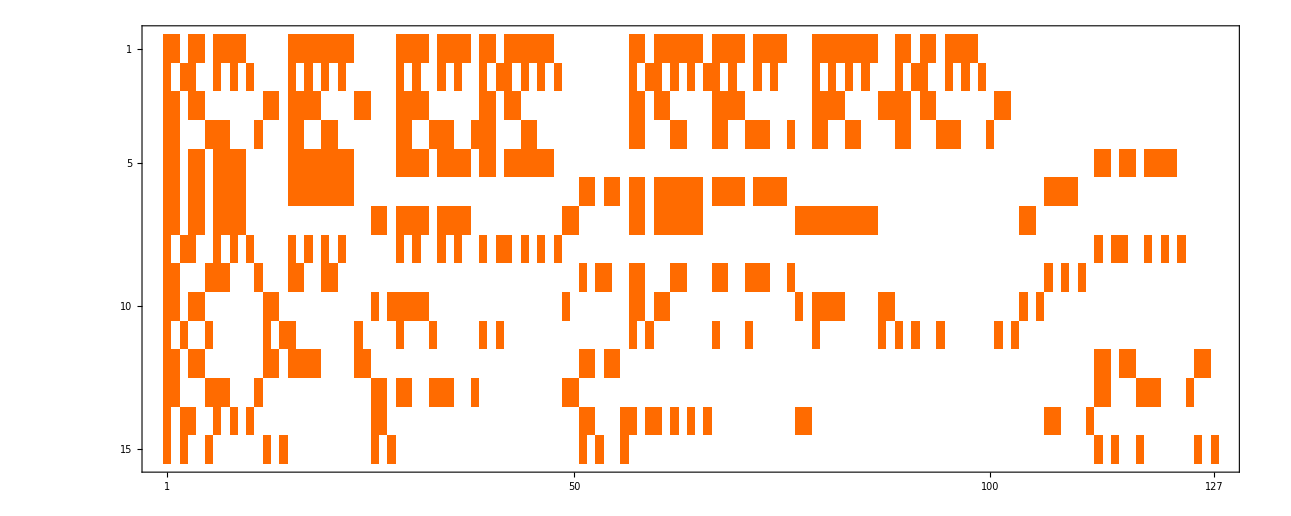

```mathematica
With[
{range=Sort[Keys[allGraphs4]],range2=Sort[allGraphs4AtomKeys,CompKey]},
Table[Table[allGraphs4[k,"colofourvector"].allGraphs4[j,"colofourvector"],{j,range}],{k,range2}]//Sort
]//MatrixPlot
```

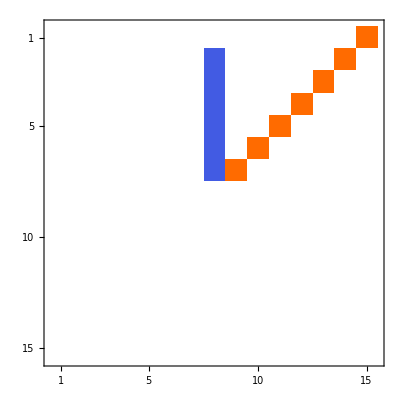

```mathematica
mmbase//Inverse//Eigenvectors//MatrixPlot
```

```mathematica
mmbase//Eigenvectors//MatrixPlot
```

-Graphics-

```mathematica
Orthogonalize[mmbase//Inverse]//MatrixPlot
```

-Graphics-

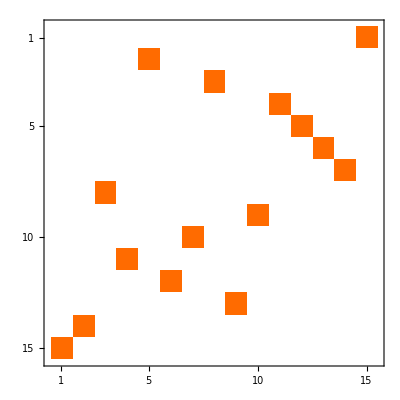

```mathematica
SchurDecomposition[N[mmbase//Inverse]][[1]]//MatrixPlot
```